{{0.05,0.00380099},{0.1,0.0147458},{0.15,0.0322209},{0.2,0.055704},{0.25,0.0847441},{0.3,0.118949},{0.35,0.157983},{0.4,0.201547},{0.45,0.249304},{0.5,0.302103},{0.55,0.360398},{0.6,0.42265},{0.65,0.481125},{0.7,0.571429},{0.75,0.666667},{0.8,0.75},{0.85,0.823529},{0.9,0.888889},{0.95,0.947368}}

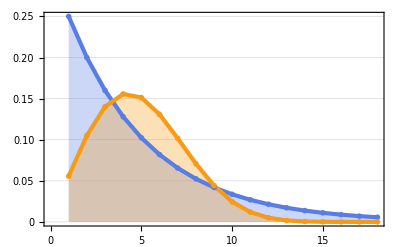

```mathematica
(*$Assumptions={0≤c≤1,Element[n,Integers]};
sol={p[n]==c*n*(1-Sum[p[i],{i,1,n-1}]),p[1]==c};
ans=RSolveValue[sol,p[n],n];*)(*p[1]:=c;p[n_]:=n c (1-Sum[p[i],{i,1,n-1}]);
Factor[p/@Range[10]];
ans=c*(-1)^(n+1)*n*Product[c*i-1,{i,1,n-1}];*)f[c_]:=Table[{n,(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]},{n,1,1/c}]
g[c_]:=Chop[Insert[f[c],{Ceiling[1/c],1-Total[Transpose[f[c]][[2]]]},-1]]
h[c_]:=1/Total[(#1[[1]]*#1[[2]]&)[Transpose[If[1/Rationalize[c]//IntegerQ,f[c],g[c]]]]]
fun=Interpolation[Table[{i,h[i]},{i,0.001,1,0.001}]];
Table[{i,InverseFunction[fun]@i},{i,0.05,0.95,0.05}]
(*p[1]:=c;p[n_]:=c(1-Sum[p[i],{i,1,n-1}]);
Factor[p/@Range[10]] foo[n_]:=c*(1-c)^(n-1) Factor[foo/@Range[10]]*)
bar[c_]:=Chop@Table[c*(1-c)^(n-1),{n,0,Length[g[InverseFunction[fun]@c]]-1}];
baz[c_]:=ListLinePlot[{bar[c],(g[InverseFunction[fun]@c]//Transpose)[[2]]},Filling->Axis,AxesOrigin->{1,0},PlotTheme->"Business"]
baz[0.2]
```

```mathematica
(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]
```

(-1)^(1+n) c^n n Pochhammer[(-1+c)/c,-1+n]

```mathematica
ExponentialGeneratingFunction[(-1)^(1+n) c^n n Pochhammer[(-1+c)/c,-1+n],n,x]
```

c x (1+c x)^(-1+1/c)

```mathematica
FullSimplify[(c Sum[n(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1],{n,1,p}])/.p->1/c,{0≤c≤1,Element[n,Integers]}]
```

ⅇ^(1/c) ExpIntegralE[-1/c,1/c]+c (-1+((-c)^(1/c) (1+ⅇ^(1/c) ExpIntegralE[1,1/c]))/Gamma[-1/c])

```mathematica
ExponentialGeneratingFunction[(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1],n,x]
```

c x (1+c x)^(-1+1/c)

```mathematica
Limit[D[c x (1+c x)^(-1+1/c),{x,1}],x->1]
```

2 c (1+c)^(-2+1/c)

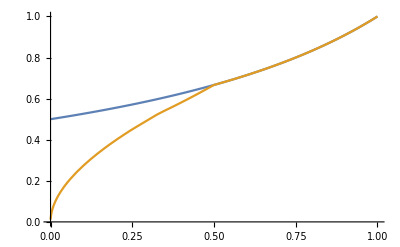

```mathematica
Plot[{1/(2-c),%91[c]},{c,0,1}]
```

```mathematica
fun
```

InterpolatingFunction[{{0.001, 1.}}, <>]

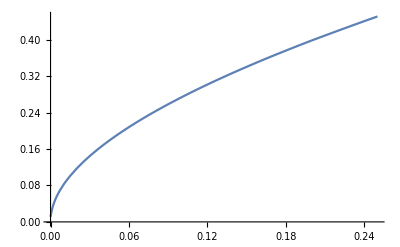

```mathematica
Plot[%91[x],{x,0,0.25}]
```

```mathematica
f[c_]:=Table[{n,(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]},{n,1,1/c}]
f[0.23]
```

{{1,0.23},{2,0.3542},{3,0.286902},{4,0.118586}}

```mathematica
f[n_]:=(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1]
g[m_]:=Sum[n(-1)^(n+1)*n*c^n*Pochhammer[(c-1)/c,n-1],{n,1,m-1}]+f[m]/c
f/@Range[5]//Expand
g/@Range[5]//Expand
```

{c,2 c-2 c^2,3 c-9 c^2+6 c^3,4 c-24 c^2+44 c^3-24 c^4,5 c-50 c^2+175 c^3-250 c^4+120 c^5}

{1,2-c,3-4 c+2 c^2,4-10 c+13 c^2-6 c^3,5-20 c+48 c^2-56 c^3+24 c^4}

```mathematica
CoefficientList[#,c]&/@(g/@Range[10]//Expand)//MatrixForm
```

({1}
{2,-1}
{3,-4,2}
{4,-10,13,-6}
{5,-20,48,-56,24}
{6,-35,133,-281,298,-120}
{7,-56,308,-1016,1922,-1884,720}
{8,-84,630,-2976,8691,-15016,13788,-5040}
{9,-120,1176,-7512,31140,-82300,131912,-114624,40320}
{10,-165,2046,-16962,94413,-351625,855592,-1287324,1066896,-362880})

```mathematica
Differences[(g/@Range[10]//Expand),1]//MatrixForm
```

(1-c
1-3 c+2 c^2
1-6 c+11 c^2-6 c^3
1-10 c+35 c^2-50 c^3+24 c^4
1-15 c+85 c^2-225 c^3+274 c^4-120 c^5
1-21 c+175 c^2-735 c^3+1624 c^4-1764 c^5+720 c^6
1-28 c+322 c^2-1960 c^3+6769 c^4-13132 c^5+13068 c^6-5040 c^7
1-36 c+546 c^2-4536 c^3+22449 c^4-67284 c^5+118124 c^6-109584 c^7+40320 c^8
1-45 c+870 c^2-9450 c^3+63273 c^4-269325 c^5+723680 c^6-1172700 c^7+1026576 c^8-362880 c^9)